```mathematica
n=100; m=1;
```

```mathematica
(*Este codigo lo puedo hacer con distincion de colores para los cuñados y hermanos tambien, en caso de ser necesario *)
```

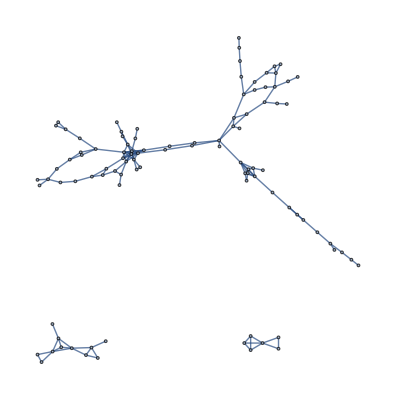

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};  scct=ConstantArray[0, n+1]; sccr=ConstantArray[0, n+1]; Do[kaux={};cc={}; x=0;  string= "D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\n0100.txt"; {spression=ToExpression[StringSplit[ReadLine[string]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine[string]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},6*n]} , m]; Graph[t]
```

```mathematica
Graph[r]
```

-Graphics-

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};  scct=ConstantArray[0, n+1]; sccr=ConstantArray[0, n+1]; Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0100.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0100.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]} , m];
```

```mathematica
(*alfa=1.0     kinship*)
```

```mathematica
Graph[t]
```

-Graphics-

```mathematica
(*alfa=1.0     random*)
```

```mathematica
Graph[r]
```

-Graphics-

```mathematica
kaux={}; cc={}; ncct=0; nccr=0; x=0; lncct={}; lnccr={}; lvd={}; lscct={}; lsccr={};  scct=ConstantArray[0, n+1]; sccr=ConstantArray[0, n+1]; Do[kaux={};cc={}; x=0;  {spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0067.txt"]]]; While[spression≠ {0,0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine["D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 6 - Maestria 1\\Trabajo Especial\\Net_Generation\\n0067.txt"]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]} , m];
```

```mathematica
(*alfa=1.5     kinship*)
```

```mathematica
Graph[t]
```

-Graphics-

```mathematica
(*alfa=1.5 random*)
```

```mathematica
Graph[r]
```

-Graphics-

```mathematica
(*Correccion de las redes random*)
```

```mathematica
(*Analisis de nuestro metodo*)
```

```mathematica
B={1,2,3};
```

```mathematica
B=Join[B, {3}]
```

{1,2,3,3}

```mathematica
B=Join[{}, {B}]
```

{{1,2,3,3}}

```mathematica
n=1000; m=20; mt=3; j=1;
MCC= GCC= A=ConstantArray[{}, mt];  s="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\RandomTest.txt"; Do[kaux={};  spression=ToExpression[StringSplit[ReadLine[s]]]; {While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}],spression=ToExpression[StringSplit[ReadLine[s]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}],  r=t,  Do[{Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], MCC[[j]]=Join[MCC[[j]], {MeanClusteringCoefficient[r]}], GCC[[j]]=Join[GCC[[j]], {GlobalClusteringCoefficient[r]}], A[[j]]=Join[A[[j]], {GraphAssortativity[r]}] } , m], j++}, mt]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

```mathematica
(*Show results*)
```

```mathematica
ListPlot[Table[A[[i]], {i,1,Length[A]}], Joined->True, PlotRange->All, Mesh->All, Frame->True, FrameStyle->Directive[Black,Bold, Large], FrameLabel->{"Times randomized", "Assortativity of random counterpart"}]
```

```mathematica
ListPlot[Table[GCC[[i]], {i,1,Length[GCC]}], Joined->True, PlotRange->All, Mesh->All, Frame->True, FrameStyle->Directive[Black,Bold, Large], FrameLabel->{"Times randomized", "GCC of random counterpart (Log)"}, ScalingFunctions->"Log"]
```

```mathematica
ListPlot[Table[MCC[[i]], {i,1,Length[MCC]}], Joined->True, PlotRange->All, Mesh->All, Frame->True, FrameStyle->Directive[Black,Bold, Large], FrameLabel->{"Times randomized", "MCC of random counterpart (Log)"}, ScalingFunctions->"Log"]
```

```mathematica
(*Analisis of random networks*)
```

```mathematica
(*Muestra de que valores usar en edges para random networks*)
```

```mathematica
n=1000; m=1;α=1000/800; 
Degrees=ConstantArray[0, n+1]; 
  string="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\RandomTest.txt";  Do[kaux={}; colors={};{spression=ToExpression[StringSplit[ReadLine[string]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine[string]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},10*α*n]} , m];
```

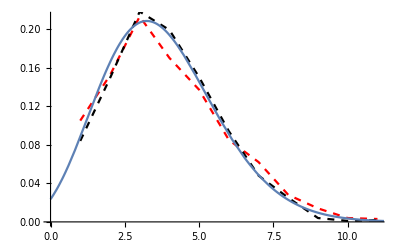

```mathematica
vd=VertexDegree[r];degrees=Table[Count[vd, i], {i,1,Max[vd]}]; degrees=degrees/n;   vd2=VertexDegree[RandomGraph[{n,3*α*n/2}]];degrees2=Table[Count[vd2, i], {i,1,Max[vd2]}]; degrees2=degrees2/n; Show[ListPlot[{degrees}, Joined->True, PlotStyle->Directive[Dashed, Red]], ListPlot[{degrees2}, Joined->True, PlotStyle->Directive[Dashed, Black]],Plot[(3*α)^(x)*Exp[-3*α]/Gamma[x+1], {x,0,20}]]
```

```mathematica
(*Conclusion, hay que crear random graphs con 3*α*n/2 edges, o sea con la funcion RandomGraph[{n,3*α*n/2}]*)
```

```mathematica
(*Codigo para analizar*)
```

```mathematica
n=1000; m=1000; α=0.1;MCC=GCC=Assort=ConstantArray[{}, 20]; For[i=0,i≤19, i++, {α=0.1+0.1*i, Do[{r=RandomGraph[{n,Round[3*(α)*n/2]}], MCC[[i+1]]=Join[MCC[[i+1]], {MeanClusteringCoefficient[r]}], GCC[[i+1]]=Join[GCC[[i+1]], {GlobalClusteringCoefficient[r]}], Assort[[i+1]]=Join[Assort[[i+1]], {GraphAssortativity[r]}]},m]}];
```

```mathematica
Length[GCC[[2]]]
```

1000

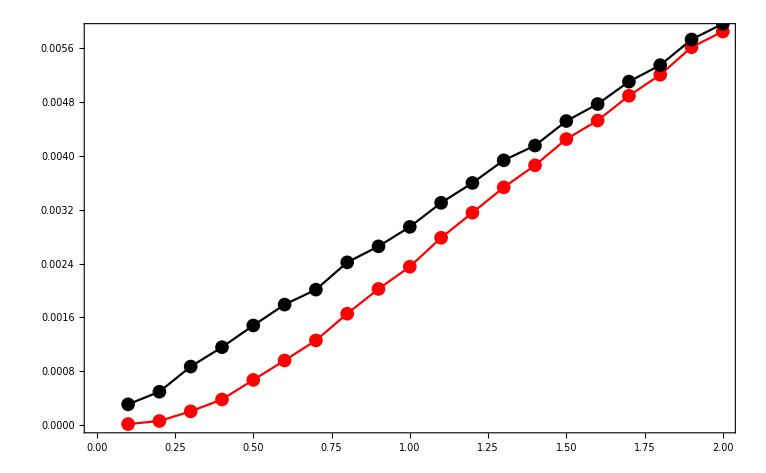

```mathematica
Show[ListPlot[Table[{i*0.1, Mean[MCC[[i]]]}, {i,1,20}], PlotStyle->Red, Joined->True, Mesh->All, Frame->True], ListPlot[Table[{i*0.1, Mean[GCC[[i]]]}, {i,1,20}], PlotStyle->Black, Joined->True, Mesh->All]]
```

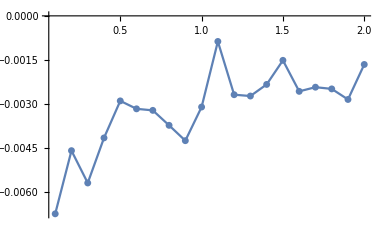

```mathematica
ListPlot[Table[{i*0.1, Mean[Assort[[i]]]}, {i,1,20}], Joined->True, Mesh->All, PlotRange->All]
```

```mathematica
(*<GCC>*)
```

```mathematica
TableForm[Table[{i*0.1, Mean[N[GCC[[i]]]], StandardDeviation[N[GCC[[i]]]], N[Mean[MCC[[i]]]], N[StandardDeviation[MCC[[i]]]]}, {i,1,20}]]
```

0.1 | 0.000305963 | 0.00432602 | 0.0000128333 | 0.000185915
0.2 | 0.00049356 | 0.00291629 | 0.0000584333 | 0.000356932
0.3 | 0.000867957 | 0.00246066 | 0.000201648 | 0.000611884
0.4 | 0.00115575 | 0.00219514 | 0.00037886 | 0.000782975
0.5 | 0.00147916 | 0.00198617 | 0.000669252 | 0.000989989
0.6 | 0.00178955 | 0.00184808 | 0.000958552 | 0.0011222
0.7 | 0.00201174 | 0.00160515 | 0.00125636 | 0.00118121
0.8 | 0.00241768 | 0.00152605 | 0.00165402 | 0.0012156
0.9 | 0.00265574 | 0.0014323 | 0.00202244 | 0.00131981
1. | 0.00294504 | 0.00134012 | 0.00235264 | 0.00127364
1.1 | 0.003303 | 0.00136777 | 0.00278336 | 0.00137576
1.2 | 0.00359832 | 0.00126293 | 0.00315536 | 0.00137863
1.3 | 0.00393512 | 0.00123274 | 0.00353271 | 0.00139443
1.4 | 0.00415439 | 0.00122327 | 0.00386053 | 0.00139976
1.5 | 0.00451879 | 0.00112526 | 0.00425083 | 0.00130912
1.6 | 0.0047718 | 0.00110967 | 0.00452649 | 0.0012788
1.7 | 0.00510508 | 0.00105176 | 0.00489453 | 0.00125611
1.8 | 0.00535004 | 0.0010562 | 0.00520683 | 0.00127777
1.9 | 0.00573179 | 0.00107204 | 0.0056167 | 0.00124621
2. | 0.00596542 | 0.000999298 | 0.0058501 | 0.00120459

```mathematica
(*<MCC>*)
```

```mathematica
TableForm[Table[{i*0.1, N[Mean[MCC[[i]]]], N[StandardDeviation[MCC[[i]]]]}, {i,1,20}]]
```

0.1 | 0. | 0.
0.2 | 0. | 0.
0.3 | 0.000593333 | 0.000976615
0.4 | 0.000593333 | 0.000651646
0.5 | 0.00284239 | 0.00121109
0.6 | 0.00500237 | 0.00197736
0.7 | 0.0068984 | 0.000688951
0.8 | 0.00852928 | 0.00137674
0.9 | 0.0112071 | 0.00104673
1. | 0.0139015 | 0.000970739
1.1 | 0.0167779 | 0.000440101
1.2 | 0.020356 | 0.000547865
1.3 | 0.0239892 | 0.000536762
1.4 | 0.0276107 | 0.000435809
1.5 | 0.0318358 | 0.000379184
1.6 | 0.036662 | 0.000533476
1.7 | 0.0411408 | 0.000399689
1.8 | 0.0463378 | 0.000321229
1.9 | 0.0519155 | 0.000234912
2. | 0.0572941 | 0.000398873

```mathematica
(*<Assort>*)
```

```mathematica
TableForm[Table[{i*0.1, N[Mean[Assort[[i]]]], N[StandardDeviation[N[Assort[[i]]]]]}, {i,1,20}]]
```

0.1 | -0.00672806 | 0.0791978
0.2 | -0.00458146 | 0.0577094
0.3 | -0.00567973 | 0.0466194
0.4 | -0.00414841 | 0.0387662
0.5 | -0.00289008 | 0.0367773
0.6 | -0.00315991 | 0.032793
0.7 | -0.00321221 | 0.0307524
0.8 | -0.00372056 | 0.0288702
0.9 | -0.00424204 | 0.0270487
1. | -0.00309847 | 0.0246756
1.1 | -0.000870175 | 0.0236646
1.2 | -0.00267956 | 0.0232341
1.3 | -0.00272499 | 0.0222695
1.4 | -0.00233038 | 0.0215882
1.5 | -0.00151197 | 0.0211268
1.6 | -0.00256565 | 0.0206475
1.7 | -0.00242455 | 0.0194518
1.8 | -0.00248248 | 0.0193898
1.9 | -0.00284161 | 0.0178638
2. | -0.00165243 | 0.0180676

```mathematica
N[StandardDeviation[N[Assort[[1]]]]]
```

0.0791978

```mathematica
(*Codigo para LCC*)
```

```mathematica
n=1000; m=100000; α=0.1;local={0, 1/3, 1/2,  2/5, 2/3}; tab=Table[ConstantArray[0, Length[local]], {i,1,20}];  For[i=0,i≤19, i++, {α=0.1+0.1*i, Do[{r=RandomGraph[{n,Round[3*(α)*n/2]}],lcc=LocalClusteringCoefficient[r], tab[[i+1]]+=Table[Count[lcc, local[[j]]], {j,1,Length[local]}]},m]}]
```

```mathematica
tab
```

{{999979,5,0,0,0},{999880,35,0,0,0},{999622,141,0,0,0},{999160,318,0,0,0},{998212,631,0,0,2},{997209,868,0,0,0},{995505,1199,0,0,1},{993130,1501,0,0,3},{990333,1830,0,0,11},{986619,2043,0,0,5},{982355,2192,0,0,8},{977267,2243,0,0,8},{970822,2418,0,0,16},{964369,2378,2,0,11},{956542,2357,2,0,15},{947479,2240,0,0,8},{937045,2127,1,0,11},{927190,2012,0,0,6},{913700,1790,0,0,13},{901230,1654,0,0,9}}

```mathematica
tab2=tab/(n*m);
```

```mathematica
TableForm[N[tab2]]
```

0.999989 | 2.56×10^-6 | 0. | 0. | 0.
0.99989 | 0.00003559 | 0. | 0. | 3.×10^-8
0.999634 | 0.00013271 | 0. | 0. | 1.×10^-7
0.999142 | 0.00031177 | 1.×10^-8 | 0. | 3.7×10^-7
0.99833 | 0.00056238 | 2.×10^-8 | 0. | 1.13×10^-6
0.997094 | 0.0008711 | 0. | 0. | 1.29×10^-6
0.995404 | 0.00119971 | 2.×10^-8 | 0. | 2.69×10^-6
0.993138 | 0.00152017 | 1.×10^-8 | 0. | 3.47×10^-6
0.990281 | 0.00180094 | 3.×10^-8 | 0. | 4.65×10^-6
0.986718 | 0.00203583 | 1.4×10^-7 | 0. | 5.94×10^-6
0.982422 | 0.00220264 | 1.×10^-7 | 0. | 7.2×10^-6
0.977263 | 0.00232221 | 1.9×10^-7 | 0. | 7.71×10^-6
0.971234 | 0.00237161 | 2.5×10^-7 | 0. | 9.36×10^-6
0.964292 | 0.00237481 | 2.5×10^-7 | 0. | 0.00001016
0.956369 | 0.00231795 | 3.6×10^-7 | 2.×10^-8 | 9.71×10^-6
0.947384 | 0.00223221 | 4.9×10^-7 | 2.×10^-8 | 0.0000104
0.937407 | 0.00210628 | 3.5×10^-7 | 1.×10^-8 | 0.00001104
0.926388 | 0.00196584 | 4.3×10^-7 | 5.×10^-8 | 0.0000104
0.914267 | 0.00181739 | 4.8×10^-7 | 5.×10^-8 | 0.0000102
0.900998 | 0.0016558 | 6.3×10^-7 | 5.×10^-8 | 9.03×10^-6

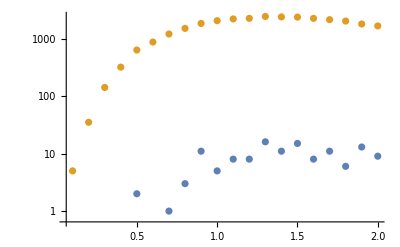

```mathematica
ListPlot[{Table[{i*0.1, tab[[i,5]] }, {i,1, 20}], Table[{i*0.1, tab[[i,2]] }, {i,1, 20}]}, ScalingFunctions->"Log", PlotRange->All]
```

```mathematica
tab=tab/Total[tab]
```

{886/889,3/889,0,0,0}

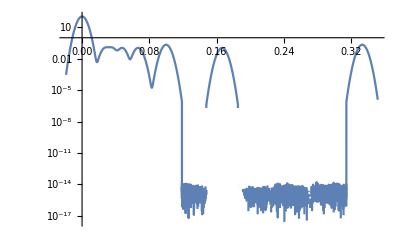

```mathematica
SmoothHistogram[LocalClusteringCoefficient[Graph[RandomGraph[{1000,Round[3*(1)*1000/2]}]]], PlotRange->All, ScalingFunctions->"Log"]
```

```mathematica
α=2.0; r=RandomGraph[{n,Round[3*(α)*n/2]}];lcc=LocalClusteringCoefficient[r];
```

```mathematica
Count[lcc, 0]
```

880

{0,1/3,1/2,2/5,2/3}

```mathematica
tab+=Table[Count[lcc, local[[i]]], {i,1,Length[local]}]
```

{2681,6,0,0,0}

```mathematica
Round[3*α*n/2]
```

150

```mathematica
Graph[r]
```

-Graphics-

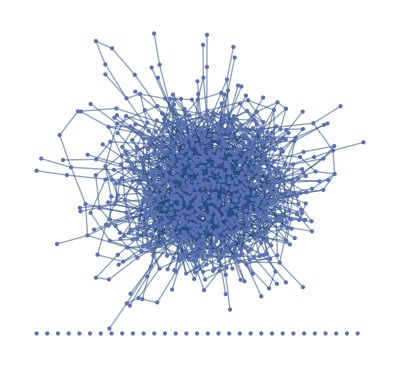

```mathematica
Graph[RandomGraph[{n,3*α*n/2}]]
```

```mathematica
degrees=Table[Count[vd, i], {i,1,Max[vd]}]; degrees=degrees/Total[degrees]
```

{15/997,48/997,86/997,127/997,156/997,158/997,155/997,119/997,62/997,46/997,19/997,5/997,1/997}

Graph[t]

```mathematica
(*marriage and blood-sibling networks*)
```

```mathematica
(*visualization of a network*)
```

```mathematica
n=100; m=1;
Degrees=ConstantArray[0, n+1]; 
  string="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\Test.txt";  Do[kaux={}; colors={};{spression=ToExpression[StringSplit[ReadLine[string]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine[string]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], colors=Table[kaux[[i,3]], {i,1,Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]} , m];
```

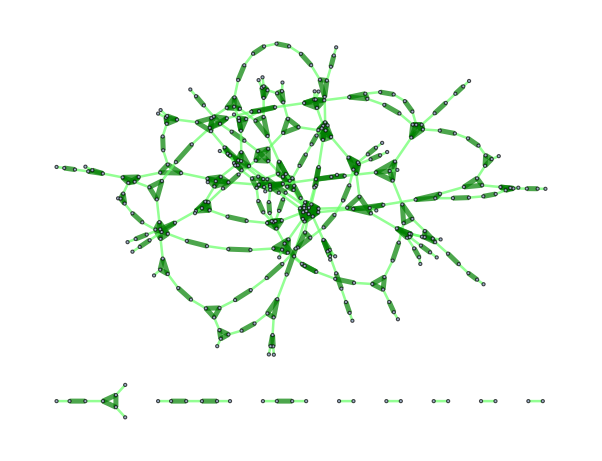

```mathematica
vect={}; Do[{If[colors[[i]]==1,vect=Join[vect, {{0.4,1,0.4}}]], If[colors[[i]]==0,vect=Join[vect, {{0,0.5,0}}]]}, {i,1,Length[colors]}]
(*Red de parentesco con dos colores, rojo para cuñados y verde para hermanos*)
T=Graph[t, EdgeStyle->Flatten[Table[t[[i]]->{RGBColor[vect[[i]]],Thickness[0.03*((1-colors[[i]])*0.1+0.1)]}, {i, 1, Length[t]}]]]
```

```mathematica
(*PDF of Vertex Degree and first two moments*)
```

```mathematica
n=1000; m=10000;
Degrees=ConstantArray[0, n+1]; 
  string="D:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre_6_-_Maestria_1\\Trabajo Especial\\Net_Generation\\MarriageTest0500.txt";  Do[kaux={}; colors={};{spression=ToExpression[StringSplit[ReadLine[string]]]; While[spression≠ {0,0, 0}, {kaux=Join[kaux, {spression}], lscct={}, lsccr={}, spression=ToExpression[StringSplit[ReadLine[string]]]}],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], lvd=VertexDegree[t], For[i=0, i≤Max[lvd], i++, {Degrees[[i]]+=Count[lvd, i]}]} , m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
λ=Mean[VertexDegree[t]]; σ=StandardDeviation[VertexDegree[t]]; Print[N[λ]]; Print[N[σ]];
```

1.216

0.446591

```mathematica
TableForm[N[Degrees/Total[Degrees]]]
```

```mathematica
vd=VertexDegree[t];
```

```mathematica
degrees=Table[{i,Degrees[[i]]}, {i,1,Length[Degrees]}];
```

```mathematica
FindDistribution[vd]
```